## Diskretne slučajne spremenljivke

1. Izpit z vprašanji izbirnega tipa vsebuje 25 vprašanj, pri vsakem so dani 4 možni odgovori. Privzemimo, da študent na vsako vprašanje odgovarja z ugibanjem. 
	a) Kolikšna je verjetnost, da študent pravilno odgovori na vsaj 20 vprašanj? 
	b) Kolikšna je verjetnost, da študent pravilno odgovori na manj kot 5 vprašanj?
	c) Poiščite pričakovano vrednost za število pravilno odgovorjenih vprašanj.
	d) Poiščite varianco za število pravilno odgovorjenih vprašanj.
	e) Poiščite standardni odklon od pričakovane vrednosti za število pravilno odgovorjenih vprašanj.
Rezultati: a) 1.24346×10^-8, b) 0.213741, c) 6.25, d) 4.6875, e) 2.16506.

```mathematica
(* Binomska porazdelitev: P(X = k) = ({{n}, {k}}) p^k (1-p)^(n-k) *)
Clear["Global`*"]
p=0.25; n=25;
(* a) *)
Binomial[n, 20]*p^20*(1-p)^5 (* verjetnost da je pravilno odgovorjeno na prvih 20 vprašanj *)
Sum[Binomial[n, k]*p^k*(1-p)^(n-k), {k,20,n}]
(* b) *)
Sum[Binomial[n, k]*p^k*(1-p)^(n-k), {k,0,4}](* k teče od 0 do 4 *)

(* c) *)
(* E(X) = n p *)
EX = n p
(* d) *)
(* Var(X) = n p (1-p) *)
VarX=n p (1-p)
(* e) *)
(* Std(X) = √(Var(X)) *)
StdX =Sqrt[VarX]
```

1.14669×10^-8

1.24346×10^-8

0.213741

6.25

4.6875

2.16506

2. Dana je slučajna spremenljivka X z verjetnostno shemo X: (2 | 3 | 5 | 8
0.2 | 0.4 | 0.3 | 0.1). Določite naslednje vrednosti:
	a) P(X <= 3), 
	b) P(X > 2.5),
	c) P(2.7 < X < 5.1),
	d) E(X),
	e) Var(X).
Rezultati: a) 0.6, b) 0.8, c) 0.7, d) 3.9, e) 3.09.

```mathematica
Clear["Global`*"]
(* a) *)
PA =0.2+0.4
(* b) *)
PB =0.4+0.3+0.1
PB=1-0.2(* isto kot zgoraj z varianto nasprotnega dogodka *)
(* c) *)
PB =0.4+0.3
(* d) *)
(* E(X) = ∑_i Subscript[x, i] Subscript[p, i] *)
EX = 2*0.2+3*0.4+5*0.3+8*0.1

(* e) *)
(* Var(X) = E(X^2) - E(X)^2 = ∑_i Subscript[x, i]^2 Subscript[p, i] - (∑_i Subscript[x, i] Subscript[p, i])^2 *)
EX2=2^2*0.2+3^2*0.4+5^2*0.3+8^2*0.1;
VarX= EX2-EX^2
```

0.6

0.8

0.8

0.7

3.9

3.09

Seznam uporabljenih ukazov za diskretne slučajne spremenljivke v programu Mathematica:
PDF[ ]
CDF[ ]
Mean[ ]
Variance[ ]
StandardDeviation[ ]
BinomialDistribution[ ]
PascalDistribution[ ]
PoissonDistribution[ ]

3. Slučajna spremenljivka ima verjetnostno shemo:    X: (-1 | 2 | 5
0.4 | 0.1 | 0.5)
	a) Narišite graf verjetnostne in porazdelitvene funkcije. 
	b) Zapišite njeno porazdelitveno funkcijo kot po kosih podano funkcijo v Mathematici. 
	c) Generirajte 100 vrednosti slučajne spremenljivke X.
	d) Določite relativne frekvence vrednosti iz zaloge vrednosti.

{0.4,0.5,1.}

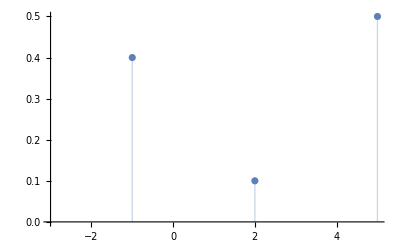

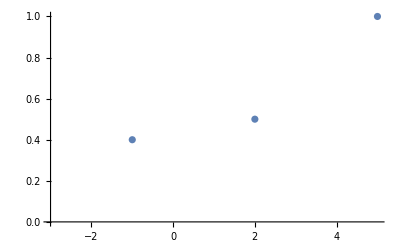

```mathematica
Clear["Global`*"]
(* Porazdelitvena funkcija: F(x) = P(X ≤ x) *)
(* a) *)
zaloga = {-1, 2, 5}; pdf = {0.4, 0.1, 0.5};
cdf = Accumulate[pdf]
ListPlot[Transpose[{zaloga,pdf}], Filling->Axis, AxesOrigin->{-3, 0}]
ListPlot[Transpose[{zaloga,cdf}], AxesOrigin->{-3, 0}]
```

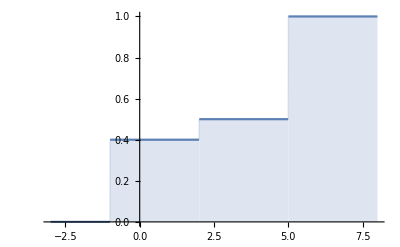

```mathematica
(* b) *)
PorF[zaloga__, cdf__, x_]:=Module[{zal=Append[zaloga, Infinity]},
 Piecewise[Table[{cdf[[i]], zal[[i]]<x&&zal[[i+1]]≥x}, {i, 1, Length[zaloga]}], 0]]
Plot[PorF[zaloga, cdf, x], {x, -3, 8}, Filling->Axis]
obratnaPorF[zaloga__, cdf__,x_]:=Piecewise[Table[{zaloga[[i+1]], cdf[[i]]<x&&cdf[[i+1]]>=x}, {i, 1, Length[cdf]-1}], First[zaloga]]
```

```mathematica
(* c) *)
realizacija[zaloga__, cdf__]:=Module[{slucajnoStevilo=Random[]}, obratnaPorF[zaloga, cdf, slucajnoStevilo]]
vzorec =Table[realizacija[zaloga, cdf], {100}]
```

{5,-1,-1,5,2,-1,-1,-1,5,5,2,-1,-1,5,-1,-1,5,-1,5,-1,5,5,5,-1,-1,5,-1,2,5,2,-1,-1,5,5,5,5,5,-1,2,5,-1,5,5,2,-1,-1,-1,2,-1,5,5,5,2,-1,5,5,5,5,5,5,-1,2,-1,-1,5,5,5,5,5,-1,5,-1,5,2,5,-1,-1,-1,-1,-1,5,5,-1,-1,5,-1,5,-1,5,5,-1,5,5,2,5,2,5,-1,5,-1}

```mathematica
(* d) *)
Count[vzorec, -1] (* prešteje število -1 v vzorcu *)

frekvence[tabela__,vrednosti__]:= Table[Count[tabela, vrednosti[[i]]], {i, 1, Length[vrednosti]}]
frekvence[vzorec, zaloga]
relFrekvence[tabela__,vrednosti__]:= frekvence[tabela, vrednosti]/Length[tabela]
relFrekvence[vzorec, zaloga] //N
```

40

{40,12,48}

{0.4,0.12,0.48}

4. Slučajna spremenljivka X ima zalogo vrednosti {1,...,20} in verjetnostno funkcijo p(n) = a/n^2. 
    a) Določite konstanto a.
    b) Narišite graf verjetnostne in porazdelitvene funkcije.
    c) V Mathematici generirajte vzorec 500 realizacij spremenljivke X in prikažite frekvence posameznih vrednosti. 
    d) Izračunajte verjetnost P(5 <= X <= 15).
    e) Izračunajte E(X), Var(X).
    f) Izračunajte E(X^3), Var(X^3).
Rezultati: a) a=0.626502, b) -, c) -, d) P(5<=X<=15)=0.0982538, e) E(X)=2.25399, Var(X)=7.44957, f) E(X^3)=131.565, Var(X^3)=435442.

0.626502

{0.626502,0.156626,0.0696114,0.0391564,0.0250601,0.0174028,0.0127858,0.0097891,0.0077346,0.00626502,0.00517771,0.00435071,0.00370711,0.00319644,0.00278445,0.00244727,0.00216783,0.00193365,0.00173546,0.00156626}

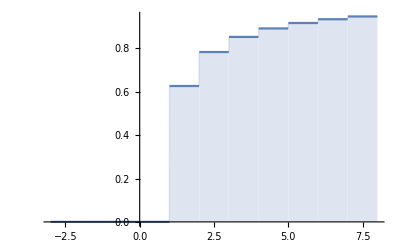

```mathematica
Clear["Global`*"]
(* a) *)
a=a/.Flatten[N[Solve[Sum[a/n^2, {n,1,20}]==1,a]]]
(* b) *)
zaloga=Range[20]; pdf= Table[a/n^2, {n,1,20}]
cdf=Accumulate[pdf];
PorF[zaloga__, cdf__, x_]:=Module[{zal=Append[zaloga, Infinity]},
 Piecewise[Table[{cdf[[i]], zal[[i]]<x&&zal[[i+1]]≥x}, {i, 1, Length[zaloga]}], 0]]
Plot[PorF[zaloga, cdf, x], {x, -3, 8}, Filling->Axis]
obratnaPorF[zaloga__, cdf__,x_]:=Piecewise[Table[{zaloga[[i+1]], cdf[[i]]<x&&cdf[[i+1]]>=x}, {i, 1, Length[cdf]-1}], First[zaloga]]
```

```mathematica
(* c) *)
realizacija[zaloga__, cdf__]:=Module[{slucajnoStevilo=Random[]}, obratnaPorF[zaloga, cdf, slucajnoStevilo]]
vzorec =Table[realizacija[zaloga, cdf], {500}];
frekvence[tabela__,vrednosti__]:= Table[Count[tabela, vrednosti[[i]]], {i, 1, Length[vrednosti]}]
frekvence[vzorec, zaloga]
relFrekvence[tabela__,vrednosti__]:= frekvence[tabela, vrednosti]/Length[tabela]
relFrekvence[vzorec, zaloga] //N
```

```mathematica
(* d) *)
(* P(5 ≤ X ≤ 15) *)
(* F(x) = P(X ≤ x) *)
F[n_]:cdf[[n]];
(* P(X ≤ 15) = F(15) *)
F[15]
(* P(5 ≤ X ≤ 15) *)
F[15]-F[4]
```

```mathematica
(* e) *)
EX= Sum[n*a/n^2, {n, 1,20}]
EX2=Sum[n^2*a/n^2, {n, 1,20}]
VarX=EX2-EX^2
StdX=Sqrt[VarX]
```

```mathematica
(* f) *)
EX3= Sum[n^3*a/n^2, {n, 1,20}]
EX6=Sum[n^6*a/n^2, {n, 1,20}]
VarX3=EX6-EX3^2
StdX3=Sqrt[VarX3]
```

131.565

452752.

435442.

659.881

5. Vržemo n igralnih kock. Slučajna spremenljivka X predstavlja največje število pik. 
    a) Izračunajte verjetnostno in porazdelitveno funkcijo slučajne spremenljivke X.
    b) Narišite graf verjetnostne in porazdelitvene funkcije.
    c) Izračunajte verjetnost P(X >= 5).
    d) Izračunajte E(X), Var(X).
Rezultati: a) -, b) -, c) P(X>=5)=0.703704, d) E(X)=4.95833, Var(X)=1.30845.

```mathematica
Clear["Global`*"]
(* a) *)
F[k_,n_]=(k/6)^n;
p[k_,n_]:=F[k,n]-F[k-1,n]
(* tabeliranje za met treh kock *)
Table[p[k,3],{k,1,6}]
```

{1/216,7/216,19/216,37/216,61/216,91/216}

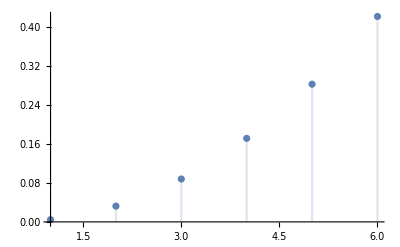

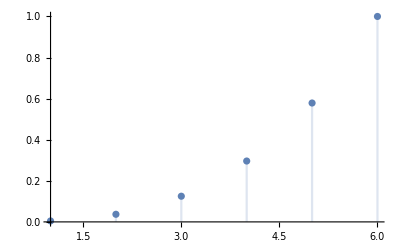

```mathematica
(* b) *)
DiscretePlot[p[k,3], {k,1,6}]
DiscretePlot[F[k,3], {k,1,6}]
```

```mathematica
(* c) *)
(* P(X≥5)= 1 - P(X < 5) = 1 - P(X ≤ 4)*)
p[5,3]+p[6,3]//N (* seštevanje verjetnostne funkcije *)
1-Sum[p[k,3],{k,1,4}]//N (* seštevanje verjetnostne funkcije *)
1-F[4,3]//N (* uporaba porazdelitvene funkcije *)
```

0.703704

0.703704

0.703704

```mathematica
(* d) *)
EX= Sum[k*p[k,3], {k, 1,6}]
EX2=Sum[k^2*p[k,3], {k, 1,6}]
VarX=EX2-EX^2 //N
StdX=Sqrt[VarX]
```

119/24

5593/216

1.30845

1.14387

6. Zavarovalni agent predstavlja zavarovalni produkt strankam na domu. Pri posameznem obisku uspešno proda zavarovalno polico z verjetnostjo 3/8. Neki dan je obiskal 6 strank. Naj slučajna spremenljivka X določa število prodanih polic za ta dan. 
	a) Zapišite porazdelitveni zakon slučajne spremenljivke X (binomska porazdelitev).
	b) Da izpolni normo, mora na dan prodati vsaj 2 polici. S kolikšno verjetnostjo bo na dani dan izponil normo?
Agent se odloči, da bo vzel dopust, ko bo prodal naslednjih 6 polic. Naj slučajna spremenljivka Y določa število obiskov na domu do dopusta. 
 	c) Zapišite porazdelitveni zakon spremenljivke Y (Pascalova porazdelitev).
 	d) Izračunajte pričakovano vrednost in varianco spremenljivke X.
 	e) Kolikšna je verjetnost, da bo moral agent pred dopustom obiskati še več kot 20 strank?
Rezultati: a) -, b) P(x>=2)=0.725819, c) -, d) E(X)=9/4, Var(X)=45/32, e) P(Y>=20)=0.223641.

{0.0596046,0.214577,0.321865,0.257492,0.115871,0.0278091,0.00278091}

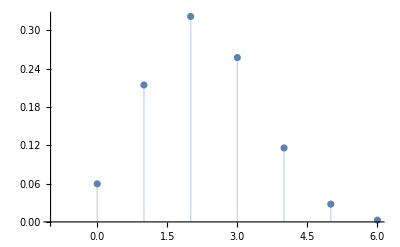

{0.0596046,0.274181,0.596046,0.853539,0.96941,0.997219,1.}

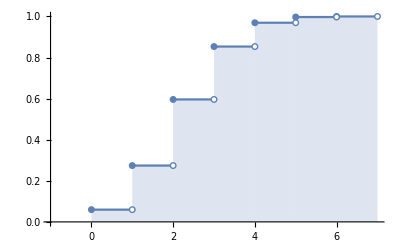

```mathematica
Clear["Global`*"]
(* a) *)
p = 3/8;
n=6;
distX=BinomialDistribution[n,p];
vfx  = Table[N[PDF[distX,k]], {k,0,6}] (* tabeliranje verjetnostne funkcije *)
ListPlot[Transpose[{Range[0,6],vfx}], AxesOrigin->{-1,0}, Filling->Axis]
pfx = Table[N[CDF[distX,k]], {k,0,6}](* tabeliranje kumulativne porazdelitvene funkcije *)
DiscretePlot[pfx[[k+1]],{k,0,6}, AxesOrigin->{-1,0}, ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
(* b)*)
(* P(X ≥ 2)= 1 - P(X ≤ 1)*)
1-CDF[distX,1] //N
1-pfx[[2]]
CDF[distX, 6]-CDF[distX, 1]//N
1-PDF[distX,0]-PDF[distX,1] //N
1-vfx[[1]]-vfx[[2]]//N
```

0.725819

0.725819

0.725819

«2 more identical outputs»

{0.00278091,0.0104284,0.0228122,0.0380203,0.0534661,0.0668326,0.076579,0.0820489,0.0833309,0.0810162,0.0759527,0.0690479,0.0611362,0.0529063,0.0448759,0.0373966,0.0306769,0.0248122,0.0198153,0.0156436,0.0122216,0.00945718,0.00725409,0.00551942,0.00416831,0.00312623,0.00232964,0.00172566,0.00127114,0.000931435,0.000679172,0.000492947,0.000356231,0.000256379,0.000183801}

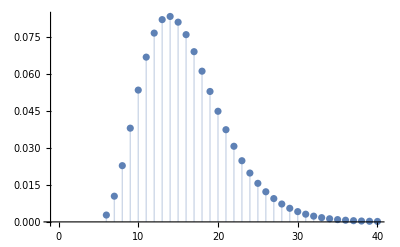

{0.00278091,0.0132093,0.0360215,0.0740418,0.127508,0.19434,0.270919,0.352968,0.436299,0.517316,0.593268,0.662316,0.723452,0.776359,0.821234,0.858631,0.889308,0.91412,0.933935,0.949579,0.961801,0.971258,0.978512,0.984031,0.9882,0.991326,0.993655,0.995381,0.996652,0.997584,0.998263,0.998756,0.999112,0.999368,0.999552}

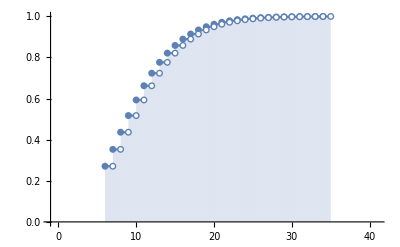

```mathematica
(* c)*)
distY=PascalDistribution[n,p];
vfy  = Table[N[PDF[distY,k]], {k,6,40}] (* tabeliranje verjetnostne funkcije *)
ListPlot[Transpose[{Range[6,40],vfy}], AxesOrigin->{-1,0}, Filling->Axis]
pfy = Table[N[CDF[distY,k]], {k,6,40}](* tabeliranje kumulativne porazdelitvene funkcije *)
DiscretePlot[pfy[[k+1]],{k,6,40}, AxesOrigin->{-1,0}, ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
(* d)*)
Mean[distX]//N
n*p
Variance[distX]//N
n*p*(1-p)
```

2.25

9/4

1.40625

45/32

```mathematica
(* e)*)
(* P(Y ≥ 20) = 1 - P(Y < 20)*)
(* moral bo obisktai vsaj 20 strank *)
1-CDF[distY, 19]//N
```

0.223641

7. Slučajna spremenljivka X naj bo binomsko porazdeljena s parametroma p=0.5 in n=10. 
	a) Izračunajte verjetnost P(X=5).
	b) Izračunajte verjetnost P(X<=2).
 	c) Izračunajte verjetnost P(X>=9).
 	d) Izračunajte verjetnost P(3<=X<5).
 	e) Izračunajte matematično upanje E(X).
 	f) Izračunajte varianco Var(X) in standardno variacijo Std(X).
Rezultati: a) P(X=5)=0.2461, b) P(x<=2)=0.0547, c) P(X>=9)=0.0107, d) P(3<=X<5)=0.3223, e) E(X)=5, f) Var(X)=2.5, Std(X)=1.58114.

```mathematica
Clear["Global`*"]
dist=BinomialDistribution[10,0.5];
(* a) *)
PDF[dist,5]
(* b) *)
CDF[dist,2]
(* c) *)
1-CDF[dist,8]
(* d) *)
CDF[dist,4]-CDF[dist,2]
(* e) *)
Mean[dist]
(* f) *)
VarX=Variance[dist]
StdX= StandardDeviation[dist]
```

0.246094

0.0546875

0.0107422

0.322266

5.

2.5

1.58114

8. Število tiskarskih napak v priročniku je slučajna spremenljivka, ki je porazdeljena po Poissonovi porazdelitvi s povprečno vrednostjo 0.01 napak na stran. Kakšna je verjetnost, da so na 100 straneh največ 3 tiskarske napake?
Rezultat: 0.9810.

```mathematica
Clear["Global`*"]
dist=PoissonDistribution[1];(* Parameter je 1 ... 100 strani * 0.01/stran *)
CDF[dist,3]//N
```

0.981012

## Zvezne slučajne spremenljivke

Seznam uporabljenih ukazov za zvezne slučajne spremenljivke v programu Mathematica:
PDF[ ]
CDF[ ]
Mean[ ]
Variance[ ]
StandardDeviation[ ]
Quantile[ ]
ProbabilityDistribution[ ]
ExponentialDistribution[ ]
GammaDistribution[ ]
NormalDistribution[ ]

9. Dana je zvezna slučajna spremenljivka z gostoto verjetnosti f(x) = c √x na intervalu [0,3].
    a) Določite obliko gostote verjetnosti in zalogo vrednosti v Mathematici.
    b) Določite normalizacijsko konstanto c. 
    c) Določite porazdelitveno funkcijo za gostoto verjetnosti f. 
    d) Narišite grafa gostote verjetnosti in porazdelitvene funkcije.
    e) Izračunajte verjetnosti P(X<2), P(1<X<2.5).
    f) Izračunajte vse tri kvartile.
    g) Generirajte 100 slučajnih vrednosti spremenljivke.

```mathematica
Clear["Global`*"]
(* a) *)
f[x_]:=c*Sqrt[x]
a=0; b=3;
```

```mathematica
(* b) *)
Clear[c]
Reduce[Integrate[f[x], {x, a, b}]==1]
```

c==1/(2 √3)

```mathematica
c=1/(2 √3);
f[x] (* gosotota verjetnosti ne vsebuje več neznane konstante *)
```

(√x)/(2 √3)

```mathematica
(* c) *)
dist = ProbabilityDistribution[f[x],{x,a, b}];
(* F(x) = (∫_a)^x f(t)dt *)
```

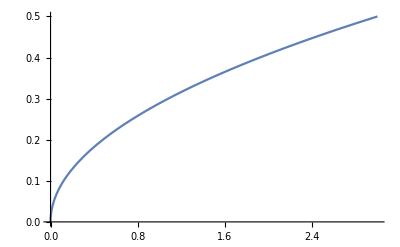

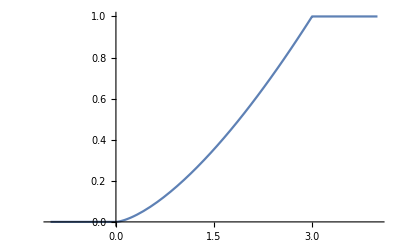

```mathematica
(* d) *)
Plot[PDF[dist,x], {x,a,b}]
Plot[CDF[dist,x], {x,-1,4}]
```

```mathematica
(* e) *)
N[CDF[dist,2]]
CDF[dist,2.5]-CDF[dist,1]
```

0.544331

0.568276

```mathematica
(* f) *)
Quantile[dist,{0.25,0.5,0.75}]
```

{1.19055,1.88988,2.47645}

```mathematica
(* g) *)
Table[3 Random[],{100}];
(* dodati je potrebno še verjetnosti *)
```

10. Slučajna spremenljivka X ima zalogo vrednosti interval [1,5] in gostoto verjetnosti p(x) = c/(x+3).  
	 a) Izračunajte konstanto c.
    b) Izračunajte porazdelitveno funkcijo X.
    c) Izračunajte verjetnost P(2<=X<=4).
    d) Izračunajte tako vrednost x, da bo veljalo P(X<=x) = 0.4.
    e) Izračunajte E(X) in Var(X).
	Naj bo še Y = ln(X). 
    f) Določi zalogo vrednosti spremenljivke Y.
    g) Izračunajte porazdelitveno funkcijo in gosototo verjetnosti slučajne spremenljivke Y.
    h) Izračunajte E(Y) in Var(Y).
Rezultati: a) a=1/ln(2), b) -, c) P(2<=X<=4)=0.485427, d) x=2.27803, e) E(X)=2.77078, Var(X)=1.32278, f) -, g) -, h) E(Y)=0.923784, Var(Y)=0.203097.

```mathematica
Clear["Global`*"]
(* a) *)
f[x_]:=c/(x+3);
a=1; b=5;
Clear[c]
Reduce[Integrate[f[x], {x, a, b}]==1]
c=c/.Flatten[N[Solve[Integrate[f[x], {x,a,b}]]==1]]
```

c==1/Log[2]

Solve::naqs: c Log[2] is not a quantified system of equations and inequalities.

Solve::naqs: 0.693147 c is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Solve[0.693147 c]==1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of c/.Solve[0.693147 c]==1..

Hold[c/.Solve[0.693147 c]==1.]

```mathematica
(* b) *)
dist = ProbabilityDistribution[f[x],{x,a, b}];
Plot[PDF[dist, x], {x,1,5}]
Plot[CDF[dist, x], {x,0,6}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of c/.Solve[0.693147 c]==1..

-Graphics-

-Graphics-

```mathematica
(* c) *)
CDF[dist, 4]-CDF[dist,2]//N
```

-1. CDF[dist,2.]+CDF[dist,4.]

```mathematica
(* d) *)
Quantile[dist, 0.4]
```

```mathematica
(* e) *)
Mean[dist]
EX = Integrate[x f[x], {x,a,b}]//N
EX2= Integrate[x^2 f[x], {x,a,b}]//N
VarX=EX2-EX^2
Variance[dist]//N
```

Mean[dist]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of c/.Solve[0.693147 c]==1..

Hold[EX=N[∫_a^b x f[x]ⅆx]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of c/.Solve[0.693147 c]==1..

Hold[EX2=N[∫_a^b x^2 f[x]ⅆx]]

-EX^2+EX2

Variance[dist]

```mathematica
(* f) *)
Log[{1,5}]
```

CDF[dist,ⅇ^y]

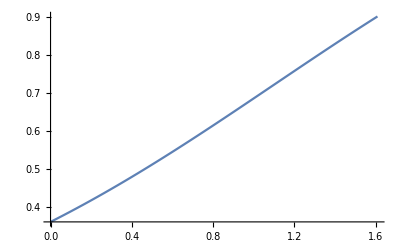

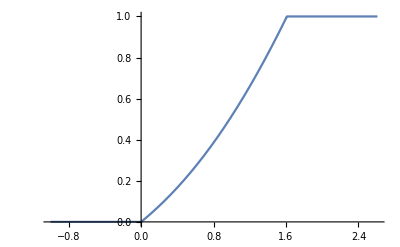

```mathematica
(* g) *)
(* Subscript[F, y]=(y) = P(Y ≤ y) = P(ln(X)≤ y) = P(X ≤ e^y) = Subscript[F, X](e^y) *)
FY[y_]:=CDF[dist,Exp[y]]
Refine[FY[y],Assumptions->{y≥0,y≤Log[5]}]
g[y_]:=-2+Log[3+ⅇ^y]/Log[2]
fY[y_]:=D[g[y],y]
distY=ProbabilityDistribution[fY[y],{y,0,Log[5]}];
Plot[PDF[distY,y], {y,0,Log[5]}]
Plot[CDF[distY,y], {y,-1,Log[5]+1}]
```

```mathematica
(* h) *)
Mean[distY]//N
Variance[distY]//N
```

0.923784

0.203097

11. Čas v dnevih do okvare stroja na neki proizvodni liniji je porazdeljen eksponentno s parametrom λ = 1/30. 
	a) Zapišite porazdelitveni zakon (zalogo vrednost in gostoto verjetnosti) za slučajno spremenljivko T, ki pomeni čas do prve okvare stroja. 
	b) Kolikšna je verjetnost, da do okvare ne bo prišlo v naslednjih 30 dneh?
	c) Denimo, da že 10 dni ni bilo okvare stroja. Kolikšna je verjetnost, da se bo stroj pokvaril v naslednjih 10 dneh?
	d) Kako dolgih je 5% najdaljših obdobij brez okvare stroja?
Naj bo T3 čas do tretje zaporedne okvare stroja (stroj je sestavljen iz veliko sestavnih delov, zato odprava okvare na enem delu ne vpliva bistveno na pričakovani čas do naslednje okvare). 
	e) Zapišite porazdelitveni zakon (zalogo vrednost in gostoto verjetnosti) za slučajno spremenljivko T3. 
	f) Kolikšna je verjetnost, bo do tretje zaporedne okvare stroja prišlo kasneje kot v dveh mesecih?
Naj slučajna spremenljivka X predstavlja število okvar stroja v naslednjih dveh mesecih. 
	g) Zapišite porazdelitveni zakon (zalogo vrednost in gostoto verjetnosti) za slučajno spremenljivko X. 
	h) Kolikšna je verjetnost, da bo vrednost slučajne spremenljivke X manjša od 3?
Rezultati: a) -, b) 0.367879, c) 0.283469, d) 89.872, e) -, f) 0.676676, g) -, h) 0.676676.

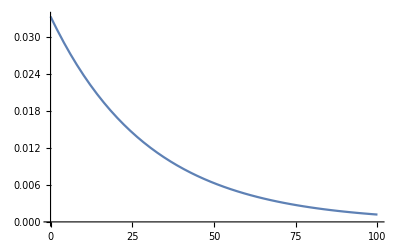

1

```mathematica
(* a) *)
(* eksponentna porazdelitev s parametrom λ=1/30 *)
distT=ExponentialDistribution[1/30];
(* zaloga vrednosti *)
a=0;b=Infinity;
(* graf gostote verjetnosti *)
Plot[PDF[distT,t],{t,0,100}]
(* preverimo. da je integral pdf enak 1 *)
Integrate[PDF[distT,t],{t,0,Infinity}]
```

```mathematica
(* b) *)
1-CDF[distT, 30]//N
```

0.367879

```mathematica
(* c) *)
CDF[distT, 10]//N
```

0.283469

```mathematica
(* d) *)
Quantile[distT,0.95]
```

89.872

```mathematica
(* e) *)
(* gama porazdelitev s parametroma alfa = 3 in beta = 1/λ = 30 *)
distT3 = GammaDistribution[3,30];
(* zaloga vrednosti *)
a1=0;b1=Infinity;
(* graf gostote verjetnosti *)
Plot[PDF[distT3,t],{t,0,100}]
```

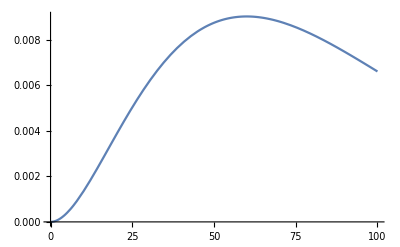

```mathematica
(* f) *)
1-CDF[distT3,60]//N
```

0.676676

{0.135335,0.270671,0.270671,0.180447,0.0902235,0.0360894,0.0120298,0.00343709,0.000859272,0.000190949}

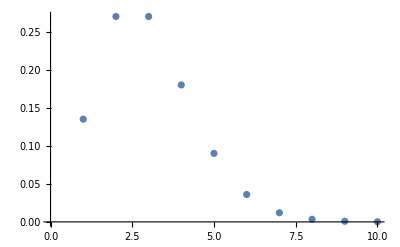

1

```mathematica
(* g) *)
(* diskretna spremenljivka, Poissonova porazdelitev, parameter lambda = 2 (pričakovani dve okvari v 60 dneh) *)
distX=PoissonDistribution[2];
(* izračun verjetnosti za napake v 60 dneh ... najverjetneje je 1 in 2 okvari *)
Table[PDF[distX, k], {k,0,9}]//N
ListPlot[Table[PDF[distX, k], {k,0,9}]]
Sum[PDF[distX, k], {k,0,Infinity}]
```

```mathematica
(* h) *)
(*  *)
CDF[distX,2]//N
```

0.676676

12. Dana je tarča s polmerom 10 cm. Vanjo mečemo pikado. Točke zadetka so enakomerno porazdeljene v tarči. (Vsaka točka ima enako gostoto verjetnosti. Predpostavimo, da tarčo zadenemo.) Naj bo R slučajna spremenljivka, ki predstavlja oddaljenost zadetka od središča tarče. 
	a) Zapišite porazdelitveno funkcijo spremenljivke R.
	b) Zapišite njeno gosototo verjetnosti.
	c) Kolikšna je verjetnost, da bomo zadeli manj kot 5 cm od središča tarče. 
	d) Izračunajte pričakovano oddaljenost zadetka od središča tarče in njeno varianco. 
Zadetki se točkujejo z 10 točkami zatetek, ki je oddaljen manj kot 1 cm od središča, 9 točk za zadetek, ki je med 1 in pod 2 cm itd. 
	e) Zapišite verjetnostno funkcijo za slučajno spremenljivko Y, ki predstavlja število doseženih točk.
	f) Poiščite pričakovano vrednost in varianco te spremenljivke.
Rezultati: a) -, b) -, c) F(5)=1/4, d) E(R)=20/3, Var(R)=50/9, Std(R)=5 √2/3, e) -, f) E(Y)=3.85, Var(Y)=5.5275, Std(Y)=2.35106.

```mathematica
Clear["Global`*"]
(* a) *)
a=0;b=10;
F[x_]:=(x/10)^2; (* porazdelitvena funk, delimo ploscino kroga s polmerom x s ploscino kroga s polmerom 10 *)
G[x_]:=Piecewise[{{0,x<0},{F[x],0≤x≤10},{1,x>10}}];
Plot[G[x],{x,-2,12}]
```

```mathematica
(* b) *)
p[x_]:=D[F[x],x]
```

```mathematica
(* c) *)
(* P(R≤5) *)
F[5]
```

1/4

```mathematica
(* d) *)
(* 1. način *)
dist=ProbabilityDistribution[p[x], {x,a,b}];
Mean[dist]
Variance[dist]
StandardDeviation[dist]
```

```mathematica
(* 2. način *)
ER = Integrate[x p[x], {x,a,b}]//N
ER2= Integrate[x^2 p[x], {x,a,b}]//N
VarR=ER2-ER^2
StdR = Sqrt[VarR]
```

6.66667

50.

5.55556

2.35702

```mathematica
(* e) *)
pp[n_]=Simplify[F[10-n+1]-F[10-n]]
tab=Table[pp[n], {n,1,10}]
Total[tab]
```

1/100 (21-2 n)

{19/100,17/100,3/20,13/100,11/100,9/100,7/100,1/20,3/100,1/100}

1

```mathematica
(* f) *)
EY = Sum[n pp[n],{n,1,10}]//N
EY2= Sum[n^2 pp[n],{n,1,10}]//N
VarY=EY2-EY^2
StdY = Sqrt[VarY]
```

3.85

20.35

5.5275

2.35106

13. Dana je slučajna spremenljivka X, ki je normalno porazdeljena s povprečno vrednostjo 10 in standardno deviacijo 2. 
	a) Izračunajte P(X < 13).
	b) Izračunajte P(X > 9).
	c) Izračunajte P(6 < X < 14).
	d) Izračunajte P(2 < X < 4). 
	e) Izračunajte P(-2 < X < 8).
	f) Določite x tako, da bo P(X < x) = 0.6.
	g) Določite x tako, da bo P(X > x) = 0.95.
Rezultati: a) 0.93319, b) 0.69146, c) 0.9545, d) 0.00135, e) 0.15866, f) 10.5067 g) 6.71029.

```mathematica
Clear["Global`*"]
dist=NormalDistribution[10,2];
(* a) *)
N[CDF[dist,13]]
(* b) *)
1-N[CDF[dist,9]]
(* c) *)
N[CDF[dist,14]] - N[CDF[dist,6]]
(* d) *)
N[CDF[dist,4]] - N[CDF[dist,2]]
(* e) *)
N[CDF[dist,8]] - N[CDF[dist,-2]]
(* f) *)
Quantile[dist,0.6]
(* g) *)
(* P(X > x) = 1 - P(X ≤ x) *)
(* P(X > x) = 0.95 <--> P(X ≤ x) = 0.05 *)
Quantile[dist, 0.05]
```

0.933193

0.691462

0.9545

0.00131823

0.158655

10.5067

6.71029

14. Čas, ki je potreben, da se celica razdeli (mitoza), je normalno porazdeljen s povprečno vrednostjo ene ure in standardno deviacijo 5 minut. 
	a) Kolikšna je verjetnost, da se celica razdeli prej kot v 45 minutah?
	b) Kolikšna je verjetnost, da celica potrebuje za delitev več kot 65 minut?
	c) Koliko časa je potrebno, da približno 99% celic zaključi z mitozo?
Rezultati: a) 0.0013499, b) 0.158655, c) 71.6317 minut.

```mathematica
Clear["Global`*"]

dist=NormalDistribution[60,5];
(* a) *)
N[CDF[dist,45]]
(* b) *)
1-N[CDF[dist,65]]
(* c) *)
Quantile[dist, 0.99]
```

0.0013499

0.158655

71.6317

15. Dana je slučajna spremenljivka X, ki je porazdeljena po eksponentni porazdelitvi s parametrom λ=2. 
	a) Izračunajte P(X <= 0).
	b) Izračunajte P(X >= 2).
	c) Izračunajte P(X <= 1).
	d) Izračunajte P(1 < X < 2). 
	e) Določite x tako, da bo P(X < x) = 0.05.
	f) Izračunajte E(X) in Var(X).
Rezultati: a) 0, b) 0.0183156, c) 0.864665, d) 0.11702, e) 0.0256466 f) E(X)=1/2, Var(X)=1/4.

```mathematica
Clear["Global`*"]
dist=ExponentialDistribution[2];
(* a) *)
N[CDF[dist,0]]
1-N[CDF[dist,2]]
N[CDF[dist,1]]
N[CDF[dist,2]]-N[CDF[dist,1]]
Quantile[dist,0.05]
Mean[dist]
Variance[dist]
```

16. Slučajna spremenljivka X je porazdeljena po eksponentni porazdelitvi s parametrom λ. Kako je porazdeljena spremenljivka Y=X^2? Zapišite porazdelitveno funkcijo in gostoto verjetnosti.

```mathematica
Clear["Global`*"]
(* Subscript[F, Y](y) = P(Y < y) = P(X^2 ≤ y) = P(X ≤ Sqrt[y]) = Subscript[F, X](Sqrt[y]) *)
pX[x_]:=PDF[ExponentialDistribution[λ],x]
pX[x]
FX[x_]:=CDF[ExponentialDistribution[λ],x]
FX[x]
FY[y_]:=Refine[FX[Sqrt[y]],Assumptions->{y>0}]
FY[y]
pY[y_]:=D[FY[y],y]
pY[y]
```

```mathematica
Integrate[ⅇ^(-x λ) λ, {t,0,x}]
D[ⅇ^(-x λ) x λ]
```

ⅇ^(-x λ) x λ